## Initial code to do step wise polymerization simulations. 14 Feb. 2022

## Periodic? Continuous Feed?

## Simulation of Step-Wise Polymerization

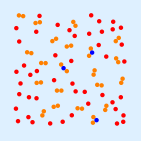
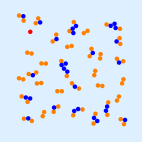
## The simulation begins with “unreacted” particles represented by the red disks and constrained to stay in the square. The particles move by random walk. If two unreacted particles collide they react: and are indicated by orange disks. Two touching orange disks represent a dimer. The unreacted particles continue their random walk and to form dimers. If one of the active particles collides with yellow (terminating) particle, it reacts and becomes the new terminating particle. The previously terminating particle becomes inert and is indicated by an blue disk: -Graphics- And the reactions proceed: -Graphics-

### The simulation will be done in two- and three- dimensions. We will use the language of two dimensions to describe the algorithm. The simulation begins with N disks representing particles constrained to a square with given side-length.

```mathematica
sideLength = 20;
```

### The particles are placed so that they don’t overlap. We can use a Hard-Core Point Process

```mathematica
proc=HardcorePointProcess[1,4,2];
(*proc=HardcorePointProcess[10,4,2]; (*3D*)*)
```

### With a specified region

```mathematica
reg =Rectangle[-sideLength{1,1}/2,sideLength{1,1}/2];
(*reg =Cuboid[-regionSize{1,1,-}/2,regionSize{1,1,1}/2]; (*3D*)*)
```

### For example:

```mathematica
particles=RandomPointConfiguration[proc,reg]["Points"];
```

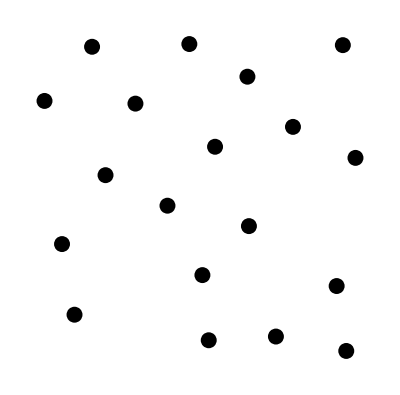

```mathematica
Graphics[Disk[#,1/2]&/@particles]
```

### We will keep track of the coordinates of three lists of particle types: active, terminating, and internal particles. Here is a graphic function that will take those three lists and draw the picture. The dimensionality of the graphics is determined by the dimensionality of the first particles coordinates.

```mathematica
polymerGraphic[{particles_,terminatingParticles_,internalParticles_}, sideLength_]:=
Block[{dimensions = Length[particles[[1]]],nSphere,plotRange, graphics},
Which[dimensions == 3, graphics = Graphics3D;nSphere = Sphere; plotRange = (sideLength/2+.5){{-1,1},{-1,1},{-1,1}},
dimensions == 2,graphics = Graphics;nSphere = Disk; plotRange = (sideLength/2+.5){{-1,1},{-1,1}},
True,Nothing
];
graphics[
{
Red,
nSphere[#,1/2]&/@particles,
Orange,
nSphere[#,1/2]&/@terminatingParticles,
Blue,
nSphere[#,1/2]&/@internalParticles
(*Opacity[0.25],*)

},
ImageSize->400,
Background->LightBlue,
Ticks->None,
PlotRange->plotRange
]
]
```

## Two Isolated Particles Combining to Form a Dimer

### Suppose we have a list of active particles:

```mathematica
activePs = Join[{{-.52,0},{.52,0}},
RandomSample[Select[RandomReal[sideLength{-1,1}/2,{12,2}],Norm[#]>6&],3]];
```

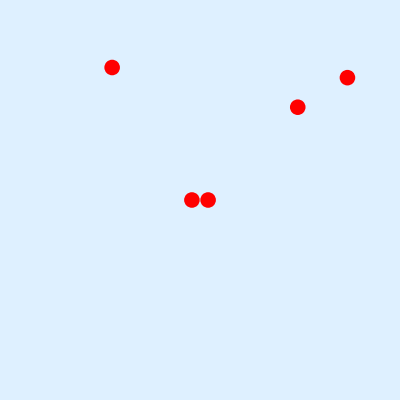

```mathematica
polymerGraphic[{activePs,{},{}},sideLength]
```

### We want the particles that are “close enough” to react and keep track of them so that we can add them to the terminating-particles list. When they react, their positions will be adjusted so that they are touching.

#### The NearestFunction is a handy and fast way to test proximity to a given point. For example:

```mathematica
activeNF = Nearest[activePs->All]
```

NearestFunction[…]

#### If we want to find the nearest particle at the position {5,5}:

```mathematica
activeNF[{5,5}]
```

{<|Element→{6.27854,5.96056},Index→4,Distance→1.59916|>}

#### If we want to find the nearest two particles to particle 5:

```mathematica
activeNF[activePs[[5]],2]
```

{<|Element→{9.47095,7.85839},Index→5,Distance→0.|>,<|Element→{6.27854,5.96056},Index→4,Distance→3.71393|>}

#### Of course, the nearest particle to particle 5 is itself--so the second member of the list is an association that tells us the location, index, and distance to particle 5. We want to query all such pairs; we can do that by feeding the NearestFunction all the positions:

```mathematica
activeNF[activePs,2]//Grid
```

<|Element→{-0.52,0},Index→1,Distance→0.|> | <|Element→{0.52,0},Index→2,Distance→1.04|>
<|Element→{0.52,0},Index→2,Distance→0.|> | <|Element→{-0.52,0},Index→1,Distance→1.04|>
<|Element→{-5.64387,8.5107},Index→3,Distance→0.|> | <|Element→{-0.52,0},Index→1,Distance→9.93409|>
<|Element→{6.27854,5.96056},Index→4,Distance→0.|> | <|Element→{9.47095,7.85839},Index→5,Distance→3.71393|>
<|Element→{9.47095,7.85839},Index→5,Distance→0.|> | <|Element→{6.27854,5.96056},Index→4,Distance→3.71393|>

#### Each row is a reaction possible reaction. The first column contains all the particles, and the second column the nearest particle. The distances in the second row give us a measure of whether the particles will react or not. There may be some redundant reactions. If particle i is nearest to particle j, then it is possible that particle j is also nearest to particle i. The redundancies will need to be removed. It is probably safe to do this by eliminating duplicate distances.

```mathematica
(With[{reactions = activeNF[activePs,3]},
DeleteDuplicates[reactions,Last[#1]["Distance"]==Last[#2]["Distance"]&]
])//Grid
```

<|Element→{-0.52,0},Index→1,Distance→0.|> | <|Element→{0.52,0},Index→2,Distance→1.04|> | <|Element→{6.27854,5.96056},Index→4,Distance→9.04148|>
<|Element→{0.52,0},Index→2,Distance→0.|> | <|Element→{-0.52,0},Index→1,Distance→1.04|> | <|Element→{6.27854,5.96056},Index→4,Distance→8.28788|>
<|Element→{-5.64387,8.5107},Index→3,Distance→0.|> | <|Element→{-0.52,0},Index→1,Distance→9.93409|> | <|Element→{0.52,0},Index→2,Distance→10.5083|>
<|Element→{9.47095,7.85839},Index→5,Distance→0.|> | <|Element→{6.27854,5.96056},Index→4,Distance→3.71393|> | <|Element→{0.52,0},Index→2,Distance→11.9111|>

#### Let’s collapse the two columns into a single Association

```mathematica
uniqueReactions =Block[
{reactions = activeNF[activePs,4], uniqueReactions},
uniqueReactions=DeleteDuplicates[reactions,Last[#1]["Distance"]==Last[#2]["Distance"]&];
Join[<|"Me"->First[#]["Index"]|>,Last[#]]&/@uniqueReactions
]
```

{<|Me→1,Element→{-5.64387,8.5107},Index→3,Distance→9.93409|>,<|Me→2,Element→{-5.64387,8.5107},Index→3,Distance→10.5083|>,<|Me→3,Element→{6.27854,5.96056},Index→4,Distance→12.1921|>,<|Me→4,Element→{-0.52,0},Index→1,Distance→9.04148|>,<|Me→5,Element→{-0.52,0},Index→1,Distance→12.7112|>}

### It is also possible that two different elements “Me” can be closest to the same “Index”, so we need to prune those reactions by splitting the reactions by their indices and then picking the closest “Me”

```mathematica
pruneReactions[reactions_]:=
Block[{splitByIndex},
If[Length[reactions]==0, Return[reactions]];
If[Length[reactions]== Length[Union[reactions[[All,"Index"]]]],
Return[reactions]
];
splitByIndex = SplitBy[reactions,#Index&];
First/@Table[SortBy[r,#Distance&],{r,splitByIndex}]
]
```

#### Then select for a given particle separation (e.g., 1.1)

```mathematica
Select[#Distance < 1.1 &][uniqueReactions]
```

{}

### We put these steps together into a single function:

```mathematica
isolatedParticleReactions[activeNF_, particles_,dx_]:= 
Block[
{reactions = activeNF[particles,2], uniqueReactions},
uniqueReactions=DeleteDuplicates[reactions,Last[#1]["Distance"]==Last[#2]["Distance"]&];
uniqueReactions=Join[<|"Me"->First[#]["Index"]|>,Last[#]]&/@uniqueReactions;
uniqueReactions= pruneReactions[uniqueReactions];
Select[#Distance < 1 + dx &][uniqueReactions]
]
```

#### We want to go through the list of reactions, move each particle so that it is touching, and keep a list of particle indices that need to turn into dimers. This function will return the new positions of all of the particles and a flat list of particles that react.

dr is a vector from “me” to “it”.  The particles move along that vector so that they touch (i.e., their distance is 1).

```mathematica
isolatedToDimer[particles_,activeNF_,dx_]:=
Block[
{positions = particles,reactions =isolatedParticleReactions[activeNF,particles,dx] , reactants},
reactants =
Flatten[
Block[{me = #["Me"],it = #["Index"],dr ,dist= #["Distance"]-1},
dr = particles[[it]]- particles[[me]];
positions[[me]] = particles[[me]] + dist dr/2;
positions[[it]] = particles[[it]] - dist dr/2;
{me,it}
]&/@reactions
];
{positions,Flatten[reactants]}
]
```

## Eliminating Collisions between Isolated Particles and Internal Particles (i.e., the non-reactive particles within a polymer chain).

#### Suppose we have a lists of active particles and internal particles

```mathematica
internalParticles = 1/(2Tan[Pi/(2 48)])AngleVector/@(Range[1,23]Pi/48);
terminatingParticles= 1/(2 Tan[Pi/(2 48)])AngleVector/@({0,24}Pi/48);
sideLength = 50;
proc=HardcorePointProcess[1,4,2];
reg =Rectangle[-sideLength{1,1}/2,sideLength{1,1}/2];
particles=Select[RandomPointConfiguration[proc,reg]["Points"], !(1/(2 Tan[Pi/(2 48)])-1< Norm[#] <1/(2 Tan[Pi/(2 48)])+1)& ];
```

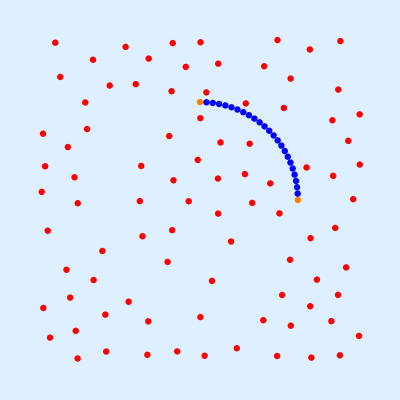

```mathematica
polymerGraphic[{particles,terminatingParticles,internalParticles}, sideLength]
```

#### We want to eliminate collisions between the random-walking isolated particles and the internal inert particles. We already have a Nearest function for the isolated particles. We can use that to test if any of them overlap by scanning over the list of internal particles. We construct a function will also two particle lists for the isolated particles—one for the positions before and one for the positions after the random step. If any isolated particle overlaps, it is returned to its original position.

```mathematica
removeInternalParticleOverlaps[internalParticles_,{particlesBefore_, particlesAfter_}, isolatedParticlesNF_]:=
Block[{eliminateRandomStep=Select[#Distance < 1 &][Flatten[isolatedParticlesNF[internalParticles]]],
particlePositions = particlesAfter
},
If[eliminateRandomStep=={},Return[particlesAfter]];
With[{indices = eliminateRandomStep[[All,"Index"]]},
particlePositions[[indices]]= particlesBefore[[indices]]
];
particlePositions
]
```

## Isolated Particles Reacting with Polymer-Terminating Particles.

#### We use a technique similar to the creation of dimers. We use the NearestFunction to scan over the terminating particles, if any of them are within a reaction distance, the isolated particle is moved so it touches the (previously) terminating particle. The function returns the new positions of the isolated particles.

#### First we use the nearest function on all the terminating particles:

```mathematica
Flatten[activeNF[terminatingParticles,1]]
```

{<|Element→{9.47095,7.85839},Index→5,Distance→9.76847|>,<|Element→{-5.64387,8.5107},Index→3,Distance→8.80838|>}

#### and then create an association that identifies the terminating particle and then select by distance:

```mathematica
terminatingParticleReactions[ terminatingParticles_,particles_,activeNF_,dx_]:= 
Block[{positions =particles,
possibleReactions = Flatten[activeNF[terminatingParticles,1]],
 terminalReactions,isolatedParticleToTerminating,terminatingParticlesToPolymer},

possibleReactions=MapIndexed[Append[#,<|"Terminator"->#2[[1]]|>]&,possibleReactions];
terminalReactions=Select[#Distance < 1 + dx &][possibleReactions];
If[Length[terminalReactions]==0,Return[{positions,{},{}}]];
terminalReactions = pruneReactions[terminalReactions];
{isolatedParticleToTerminating,terminatingParticlesToPolymer}=
Transpose[
Block[
{terminator = #Terminator,isolated= #Index,dr,dist=#Distance },
dr =positions[[isolated]]- terminatingParticles[[terminator]];
positions[[isolated]] -= (dist-1) dr;
{isolated,terminator}
]&/@terminalReactions
];
{positions,isolatedParticleToTerminating,terminatingParticlesToPolymer}
]
```

## Update all particles

#### The above steps are combined into a function to update all of the particles. This function creates the NearestFunction and passes it to the helper-functions we wrote above, collects the indices of particles that need to be inserted and deleted in the isolated, terminating, and internal lists, and then performs those insertions and deletions

Everything we have done doesn’t depend on the dimensionality of the space.  The only thing that matters is how we take the random step.
We can use the dimensionality of the first active particle to determine that.

```mathematica
updateParticles[{activeParticles_,terminatingParticles_,internalParticles_}, dx_, domainSize_]:= 
Block[
{
newTerminatingParticles=terminatingParticles,
newInternalParticles=internalParticles,
newActiveParticlePositions ,
remainingActiveParticles,
isolatedParticleToDimers={},
isolatedParticleToTerminating={},
terminatingParticlesToPolymer={},
activeNF,
nSphere,domain
},
If[Length[activeParticles]<= 1,Return[{activeParticles,terminatingParticles,internalParticles}]];

Which[
Length[activeParticles[[1]]]==2,nSphere=Circle,
Length[activeParticles[[1]]]==3,nSphere=Sphere,
True,Echo[""]
];

newActiveParticlePositions = Clip[
activeParticles+ dx RandomPoint[nSphere[],Length[activeParticles]],
domainSize{-1,1}
];

activeNF= Nearest[newActiveParticlePositions->All];

{newActiveParticlePositions,isolatedParticleToDimers}=isolatedToDimer[newActiveParticlePositions,activeNF,dx];

If[Length[internalParticles]>0,
newActiveParticlePositions = removeInternalParticleOverlaps[internalParticles,{activeParticles,newActiveParticlePositions},activeNF]
];

If[Length[terminatingParticles]>0,
{newActiveParticlePositions,isolatedParticleToTerminating,terminatingParticlesToPolymer}=
terminatingParticleReactions[terminatingParticles,newActiveParticlePositions,activeNF,dx]
];

{displayisolatedParticleToTerminating,displayterminatingParticlesToPolymer}=
{isolatedParticleToTerminating,terminatingParticlesToPolymer};


If[
(isolatedParticleToDimers== {} && isolatedParticleToTerminating== {}),
Return[{newActiveParticlePositions,newTerminatingParticles,newInternalParticles}]
];


remainingActiveParticles  =Delete[newActiveParticlePositions,List/@Catenate[{isolatedParticleToDimers,isolatedParticleToTerminating}]];


If[Length[terminatingParticlesToPolymer]!=0,
displaynewInternalParticles= terminatingParticlesToPolymer;
newInternalParticles = (*move terminating particles that reacted to internal*)
Union@Catenate[{newInternalParticles,newTerminatingParticles[[terminatingParticlesToPolymer]]}];
newTerminatingParticles= Union@Catenate[
{newActiveParticlePositions[[isolatedParticleToTerminating]],
Delete[newTerminatingParticles,List/@terminatingParticlesToPolymer]}];
];

If[Length[isolatedParticleToDimers] != 0,(*add isolated particles that reacted, delete those that moved to internal*)
newTerminatingParticles= 
Catenate[{
newActiveParticlePositions[[Union@Flatten[{isolatedParticleToDimers,isolatedParticleToTerminating}]]],
newTerminatingParticles
}]
];

{remainingActiveParticles,newTerminatingParticles,newInternalParticles}
]
```

## Simulation Example 2D

```mathematica
sideLength = 50;
proc=HardcorePointProcess[10,2,2];
reg =Rectangle[-sideLength{1,1}/2,sideLength{1,1}/2];
particles=RandomPointConfiguration[proc,reg]["Points"]//Quiet;
internalParticles={};
terminatingParticles={};
graphic = polymerGraphic[{particles,terminatingParticles,internalParticles}, sideLength];
```

```mathematica
Dynamic[graphic]
```

```mathematica
While[Length[particles]> 1,
{particles,terminatingParticles,internalParticles}= updateParticles[{particles,terminatingParticles,internalParticles},.2,sideLength/2];
graphic = polymerGraphic[{particles,terminatingParticles,internalParticles}, sideLength]
]
```

## Simulation Example 3D

```mathematica
sideLength = 25;
proc=HardcorePointProcess[10,2,3];
reg =Cuboid[-sideLength{1,1,1}/2,sideLength{1,1,1}/2];
particles=RandomPointConfiguration[proc,reg]["Points"]//Quiet;
internalParticles={};
terminatingParticles={};
graphic = polymerGraphic[{particles,terminatingParticles,internalParticles}, sideLength];
```

Run the above While command again.

## Discussion

#### This simulation fails to simulate the behavior of step-wise growth and it is instructive to understand why. Experimental observations show that dimers react to form tetramers, tetramers and dimers to form hexamers, and on. Our simulation prevents these higher order reactions from occurring because only the singlets to move. In a separate chapter, we will develop an algorithm for the collective motion of polymer chains and then combine these algorithms for a better simulation of step-wise polymerization.